```mathematica
x=Import["C:\\Users\\Adam\\Downloads\\surp-2019\\nfft-hermite\\matlab\\hermpoly_asy_airy_x.mat","list"]
```

{-32 -31.99935999359993 -31.99871998719987 -31.99807998079981 -31.99743997439974 -31.99679996799968 -31.99615996159962 -31.99551995519955 -31.99487994879949 -31.994…1.99423994239942 31.99487994879949 31.99551995519955 31.99615996159962 31.99679996799968 31.99743997439974 31.99807998079981 31.99871998719987 31.99935999359994 32}
 |  |  |  |

```mathematica
x
```

{-32 -31.99935999359993 -31.99871998719987 -31.99807998079981 -31.99743997439974 -31.99679996799968 -31.99615996159962 -31.99551995519955 -31.99487994879949 -31.994…1.99423994239942 31.99487994879949 31.99551995519955 31.99615996159962 31.99679996799968 31.99743997439974 31.99807998079981 31.99871998719987 31.99935999359994 32}
 |  |  |  |

```mathematica
x[0]
```

{-32 -31.99935999359993 -31.99871998719987 -31.99807998079981 -31.99743997439974 -31.99679996799968 -31.99615996159962 -31.99551995519955 -31.99487994879949 -…23994239942 31.99487994879949 31.99551995519955 31.99615996159962 31.99679996799968 31.99743997439974 31.99807998079981 31.99871998719987 31.99935999359994 32}[0]
 |  |  |  |

```mathematica
x{0}
```

{0}

```mathematica
Head @ x
```

List

```mathematica
x[[0]]
```

List

```mathematica
x[[0]]
```

List

```mathematica
x[[3]]
```

Part::partw: Part 3 of {-32 -31.99935999359993 -31.99871998719987 -31.99807998079981 -31.99743997439974 -31.99679996799968 -31.99615996159962 -31.99551995519955 -31.99487994879949 -31.9942399…36 31.99423994239942 31.99487994879949 31.99551995519955 31.99615996159962 31.99679996799968 31.99743997439974 31.99807998079981 31.99871998719987 31.99935999359994 32} does not exist.

{-32 -31.99935999359993 -31.99871998719987 -31.99807998079981 -31.99743997439974 -31.99679996799968 -31.99615996159962 -31.99551995519955 -31.99487994879949 -…23994239942 31.99487994879949 31.99551995519955 31.99615996159962 31.99679996799968 31.99743997439974 31.99807998079981 31.99871998719987 31.99935999359994 32}⟦3⟧
 |  |  |  |

```mathematica
x=Import["C:\\Users\\Adam\\Downloads\\surp-2019\\nfft-hermite\\matlab\\hermpoly_asy_airy_x.mat","list"]
```

{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99982,31.9949,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}
 |  |  |  |

```mathematica
x[[0]]
```

List

```mathematica
x[0]
```

{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99983,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}[0]
 |  |  |  |

```mathematica
x+1
```

{-31,-30.9994,-30.9987,-30.9981,-30.9974,-30.9968,-30.9962,-30.9955,-30.9949,99982,32.9949,32.9955,32.9962,32.9968,32.9974,32.9981,32.9987,32.9994,33}
 |  |  |  |

```mathematica
f[x_]:=x^2
```

```mathematica
f[x]
```

{1024,1023.96,1023.92,1023.88,1023.84,1023.8,1023.75,1023.71,1023.67,99983,1023.71,1023.75,1023.8,1023.84,1023.88,1023.92,1023.96,1024}
 |  |  |  |

```mathematica
HermiteH[500,0]
```

377417592221683502036865134204816120301622229363894166592887721921744588137792862306856818979544009437179007998409814837972661705792675155791947694723619746710556703848377975964637399649313381120750234724991524489488294500276852773918850186560918838230568235779349576671635209831905721310948915399707305574854387728086356239370128466857032846423614157875633723939344522135633164580258038322031786273522795625687202552083488334879877156128704263701887858732944900239554489479106454541743076651344229660317580604074443841143528038873372900590571613564545515392588480885427622694092800000000000000000000000000000000000000000000000000000000000000

```mathematica
h[n_,x_]:=HermiteH[n,x]/sqrt[sqrt[Pi]*2^n*n!]
```

```mathematica
h[500,0]
```

377417592221683502036865134204816120301622229363894166592887721921744588137792862306856818979544009437179007998409814837972661705792675155791947694723619746710556703848377975964637399649313381120750234724991524489488294500276852773918850186560918838230568235779349576671635209831905721310948915399707305574854387728086356239370128466857032846423614157875633723939344522135633164580258038322031786273522795625687202552083488334879877156128704263701887858732944900239554489479106454541743076651344229660317580604074443841143528038873372900590571613564545515392588480885427622694092800000000000000000000000000000000000000000000000000000000000000/sqrt[3993984426547508861305390944632658769491465612732950884149352264463669653783918786673855847931586297648724730100712687233287867670033234347147721372160052970468852277435367085064790343283345982785772859940510918528070095138370429504769382461652184670792668564749747182728979673007824853940403174783379461981377594688094308995249697607727579137178606555069217194222363439778224206578431466544196150784271265561123088538027593033553551529401457853649535775425729310701035075686547366124355050660879155316288666973553745148520593257875601748532607163260780959394611457161826005390022163500384517756609464749567995251111398216507373580124815177400601722590893150586590359116008988749851761693190689228238008607755225687337923116872708482175000550889761043932312692198817965575874482087355854957667093854984963161313376186755900436597903368883575958968256738241094038338021793478788394592854525976460113138953893460202621461412466767406873753554433304755169025189150527313391959692691048456575394801454926197688818611863300874422358915700504682504830680617901494815422107753552276905563018887609770664552859008696057852779541484186292035509861625299662585190825328640000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 sqrt[π]]

```mathematica
h[n_,x_]:=HermiteH[n,x]/Sqrt[Sqrt[Pi]*2^n*n!]
```

```mathematica
N[h[500,0]]
```

0.141851

```mathematica
x
```

{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99982,31.9949,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}
 |  |  |  |

```mathematica
Y=N[h[500,x]]
```

{1.2544×10^221,1.23318×10^221,1.21232×10^221,1.19181×10^221,1.17164×10^221,1.15181×10^221,99988,1.15181×10^221,1.17164×10^221,1.19181×10^221,1.21232×10^221,1.23318×10^221,1.2544×10^221}
 |  |  |  |

```mathematica
h[500,32]
```

(11246171067381937218644228276886421956064341584249056511658806161373776366619783597715830519222389831717818535493619099806037852123795839001071093207285190655913190631970783278355070860530893853479422172526103036434327128353287051902344057882390368268998133055488578977736883085689612808513181266372359823685372017859188828585275388736993047310697345213061596478078601964413638471398412101653668592933717193935939134034910672274968462988934715571116072085865668198519287733284647384524840110710177020507846874422461160061246251027164424887635131910264904168091066233620436926545281480684485083453805290157265069164155804144364828794229683325391845332806919073693208548884688377451219733913436185243450325927745345633118102222657130600191670396660439657428394512884829111259294918178433 √(349/369093519934555071778842377468569025218475055980733708421322404397281980823706337780139079614827576204121246623681042386278749242701443568461))/(65482535327350437471689690500578697540150877004796578611575344481093791652605656839007545860281252039942211468090134896728677595544556580070150230333528944456086253886386809064331387432350606488190374622603191771714442537887800820607365523266809197409851632635508806930656938374831955886043828818608531894872688917258114285329692969881059123144603077664300410294624674997125375968912831269067692112055222019648502355151872852806860800000000000000000000000000000000000000000000000000000000000000 π^(1/4))

```mathematica
N[h[500,32]]
```

1.2544×10^221

```mathematica
HermiteH[500,32]
```

333754312678984487415746300060100508906498590155829513682568519710686953593124028985220890430165986511577659389154756340796522058505421785623497783376734508901604021836281061822508302636632656109016513257911539788990097827670536746623602525064424716224321830610674547821697958684678479903104700379514617793131938818221286144284191070130136041059320063740590293134980470013533715336838580397561198844873085085590531850920886662152909508084464445943083027180348361284696045534553495374180887231365081107406703773618284227793330146909561268744309984174795519175886899517744317278183378310570262185218094217948915051930325540708198178762580251240004280872659803227394653609555361303277109555690336009062102819124253343696375757956911242908509582574619802376394089578039993234240793081065834457792958948680544225193133073010597324940814758371344362466573383710724325376

```mathematica
ScientificForm[N[%24,864]]
```

3.33754312678984487415746300060100508906498590155829513682568519710686953593124028985220890430165986511577659389154756340796522058505421785623497783376734508901604021836281061822508302636632656109016513257911539788990097827670536746623602525064424716224321830610674547821697958684678479903104700379514617793131938818221286144284191070130136041059320063740590293134980470013533715336838580397561198844873085085590531850920886662152909508084464445943083027180348361284696045534553495374180887231365081107406703773618284227793330146909561268744309984174795519175886899517744317278183378310570262185218094217948915051930325540708198178762580251240004280872659803227394653609555361303277109555690336009062102819124253343696375757956911242908509582574619802376394089578039993234240793081065834457792958948680544225193133073010597324940814758371344362466573383710724325376×10^863

```mathematica
Y
```

{1.2544×10^221,1.23318×10^221,1.21232×10^221,1.19181×10^221,1.17164×10^221,1.15181×10^221,99988,1.15181×10^221,1.17164×10^221,1.19181×10^221,1.21232×10^221,1.23318×10^221,1.2544×10^221}
 |  |  |  |

```mathematica
hp[n_,x_]:=h[n,x]*Exp[-x^2/2]
```

```mathematica
Yp=hp[500,x]
```

{1/1 1124617106738193721864422827688642195606434158424905651165880616137364811810222265713060019167039666043965742839451288482911125929491817843311,0.0550993,99996,0.0550993,112461710673819372186447398482911125929491817843311/1}
 |  |  |  |

```mathematica
Yp=N[Yp]
```

{0.0549113,0.0550993,0.0552879,0.055477,0.0556666,0.0558568,0.0560475,99986,0.0560475,0.0558568,0.0556666,0.055477,0.0552879,0.0550993,0.0549113}
 |  |  |  |

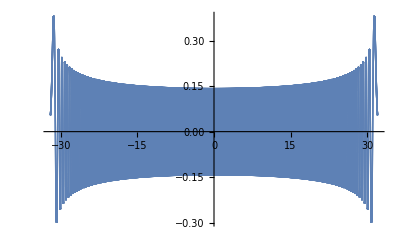

```mathematica
ListPlot[Transpose[{x,Yp}]]
```

```mathematica
Export["out1",Yp,"List"]
```

out1

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["out1"]]]
```

```mathematica
hp[500,x]
```

{1/1 1124617106738193721864422827688642195606434158424905651165880616137364811810222265713060019167039666043965742839451288482911125929491817843311,0.0550993,99996,0.0550993,112461710673819372186447398482911125929491817843311/1}
 |  |  |  |

```mathematica
Ypa:=Abs[Yp]
```

```mathematica
Ypa
```

{0.0549113,0.0550993,0.0552879,0.055477,0.0556666,0.0558568,0.0560475,99986,0.0560475,0.0558568,0.0556666,0.055477,0.0552879,0.0550993,0.0549113}
 |  |  |  |

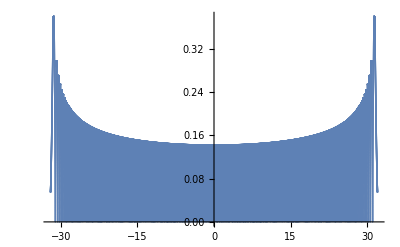

```mathematica
ListPlot[Transpose[{x,Ypa}]]
```

```mathematica
hp
```

hp

```mathematica
hp[512,0]
```

```mathematica
Expo
```

hp[512,0]

```mathematica
h[500,0]
```

h[500,0]

```mathematica
h[n_,x_]:=HermiteH[n,x]/Sqrt[Sqrt[Pi]*2^n*n!]
```

```mathematica
h[500,0]
```

(119 √128813638457159720050815989736530589801247794537276064239041519134651411307473511885268538785574824095238315071664683792811283485702803805392889)/(226156424291633194186662080095093570025917938800079226639565593765455331328 π^(1/4))

```mathematica
hp[n_,x_]:=h[n,x]*Exp[-x^2/2]
```

```mathematica
hp[512,0]
```

(91 √28532381545403026505796665260909696261213060961386419670168389032337040836648116220544034514796174373255490359161573177172211973593980779335120551387)/(57896044618658097711785492504343953926634992332820282019728792003956564819968 √2 π^(1/4))

```mathematica
N[hp[512,0]]
```

0.141013

```mathematica
N[hp[512,-32]]
```

0.262461

```mathematica
x
```

x

```mathematica
x=Import["C:\\Users\\Adam\\Downloads\\surp-2019\\nfft-hermite\\data\\x.mat","list"]
```

{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99982,31.9949,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}
 |  |  |  |

```mathematica
size[x]
```

size[{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99982,31.9949,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}]
 |  |  |  |

```mathematica
Length[x]
```

100000

```mathematica
y256=N[hp[256,x]]
```

{7.48205×10^-61,7.59124×10^-61,7.70201×10^-61,7.81439×10^-61,7.92841×10^-61,8.04409×10^-61,8.16145×10^-61,99987,8.04409×10^-61,7.92841×10^-61,7.81439×10^-61,7.70201×10^-61,7.59124×10^-61,7.48205×10^-61}
 |  |  |  |

```mathematica
N[hp[256,-32]]
```

7.48205×10^-61

```mathematica
y512=N[hp[512,x]]
```

{0.262461,0.262929,0.263397,0.263864,0.264331,0.264799,0.265266,0.265733,99984,0.265733,0.265266,0.264799,0.264331,0.263864,0.263397,0.262929,0.262461}
 |  |  |  |

```mathematica
Export["mathematica_yp_y256.mat",y256,"List"]
```

mathematica_yp_y256.mat

```mathematica
Export["mathematica_yp_y512.mat",y512,"List"]
```

mathematica_yp_y512.mat

```mathematica
x=Import["C:\\Users\\Adam\\Downloads\\surp-2019\\nfft-hermite\\data\\x.mat","list"]
```

{-32,-31.9994,-31.9987,-31.9981,-31.9974,-31.9968,-31.9962,-31.9955,-31.9949,99982,31.9949,31.9955,31.9962,31.9968,31.9974,31.9981,31.9987,31.9994,32}
 |  |  |  |

```mathematica
h[n_,x_]:=HermiteH[n,x]/Sqrt[Sqrt[Pi]*2^n*n!]
```

```mathematica
hp[n_,x_]:=h[n,x]*Exp[-x^2/2]
```

```mathematica
N[hp[500,0]]
```

0.141851

```mathematica
p_
```

```mathematica
y=N[hp[192,x]]
```

{6.44881×10^-88,6.55409×10^-88,6.66109×10^-88,6.76983×10^-88,6.88034×10^-88,6.99266×10^-88,7.1068×10^-88,99987,6.99266×10^-88,6.88034×10^-88,6.76983×10^-88,6.66109×10^-88,6.55409×10^-88,6.44881×10^-88}
 |  |  |  |

```mathematica
Export["mathematica_hp_y192.mat",y,"List"]
```

mathematica_hp_y192.mat

```mathematica
Export["mathematica_hp_y192.mat",y,"List"]
```

mathematica_hp_y192.mat